(((ⅇ^(32 (x^2+y^2))+1024 y^2) √(1+1024 ⅇ^(-32 (x^2+y^2)) (x^2+y^2)))/(ⅇ^(32 (x^2+y^2))+1024 (x^2+y^2)) | -(1024 ⅇ^(-32 (x^2+y^2)) x y)/(√(1+1024 ⅇ^(-32 (x^2+y^2)) (x^2+y^2)))
-(1024 ⅇ^(-32 (x^2+y^2)) x y)/(√(1+1024 ⅇ^(-32 (x^2+y^2)) (x^2+y^2))) | ((ⅇ^(32 (x^2+y^2))+1024 x^2) √(1+1024 ⅇ^(-32 (x^2+y^2)) (x^2+y^2)))/(ⅇ^(32 (x^2+y^2))+1024 (x^2+y^2)))

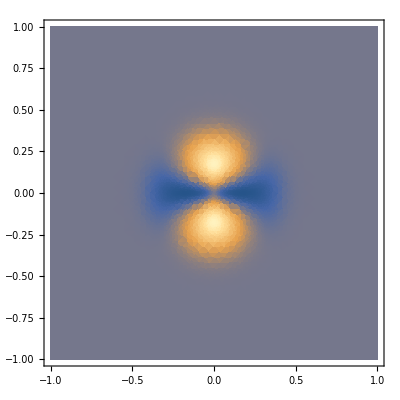
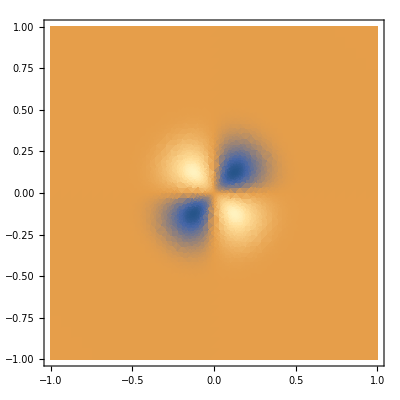
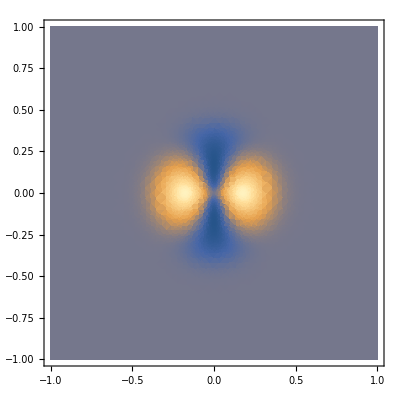
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
a=1/4;
vars={x,y};
S={x,y,Exp[-(x^2+y^2)/a^2]};
J=Outer[D,S,vars];
G=Transpose[J].J;
A=FullSimplify[Sqrt[Det[G]]Inverse[G]];
A//MatrixForm
Map[DensityPlot[#,{x,-1,1},{y,-1,1},PlotRange->Full,PlotPoints->32,MaxRecursion->5]&,Flatten[A]]
```